Last modified on: Monday, July 9, 2018 at 10:31

Author Info

Sumner Magruder

Markus van Almsick

University Hamburg

Poster Session Content

Relationship of System Symbols for Wolfram Language modeling

Extract information and code examples of the Wolfram Language

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics-

GitHub was crawled for Mathematica Notebook from which the conditional distribution of system symbols have been generated

Apply a Language model on notebook cells

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Section Header

Type text here

Crawl GitHub

githubResults=SearchRepositories["Mathematica"];
(*8586 public repositories with language(s):Mathematica. Only first 1000 repositories available via public API*)

notebookResults=SearchNotebooks[Normal[githubResults[All,"full_name"]]];
files=DownloadRawURLs[notebookResults,CreateDirectory[]]
(*3524 requests must be made.*)

Occurrences of System Symbols in GitHub notebooks

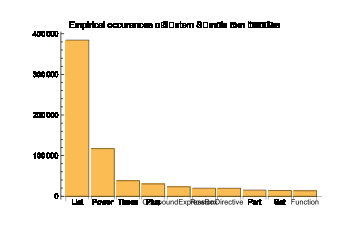

Searching the connections via maximum probability at each step

Given the PDF and conditional PDF of System Symbols, we can search for chains of symbols.
Note: taking what is most likely at each step is not necessarily the best approach. Beam search may yield better results.

NestList[nextSymbol[#]&,Range,3]
(*{Range,Length,Part}*)

Which means that it is common in Wolfram Language code to see something like:

Range[Length[myData[[n]]]]

NestList[nextSymbol[#]&,Import,3]
(*{Import,StringJoin,NotebookDirectory}*)

Which means that it is common in Wolfram Language code to see something like:

Import[StringJoin[NotebookDirectory[],...]]

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

Crawled the accessible 1000 out of 8,586 repositories on GitHub tagged with Mathematica as a language therein. Subsequently those repositories were searched for `.nb` files from which 3,524 Mathematica notebooks were retrieved. With assistance of Carl Woll, non system symbols were replaced with the general placeholder NonWolfram and a replacement rule extracted the relationship of System Symbols (+ NonWolfram) as Head. From which, this empirical PDF and conditional distribution were derived.

#### Code

Provide one of:

https://github.com/SumNeuron/WSS2018

#### Written Content / Lesson Plans

#### Conclusions in Detail

#### All Visualizations

#### Data Sources Links/References

#### Future Directions

Take the cells of the retrieved notebooks and put them into a language model and putatively feed in the distribution information.

#### Background Info Links/References

#### Keywords

Provide keywords as items

GitHub

WolframLanguage

#### Other information